```mathematica
data:={{-15,-0.008,0.1,0.001},{-14,-0.007,0.1,0.001},{-13,-0.006,0.1,0.001},{-12,-0.005,0.1,0.001},{-11,-0.003,0.1,0.001},{-10,-0.002,0.1,0.001},{-9,-0.001,0.1,0.001},{-8,0.002,0.1,0.001},{-7,0.003,0.1,0.001},{-6,0.004,0.1,0.001},{-5,0.005,0.1,0.001},{-4,0.006,0.1,0.001},{-3,0.007,0.1,0.001},{-2,0.008,0.1,0.001},{-1,0.009,0.1,0.001},{0,0.01,0.1,0.001},{0.05,0.01,0.005,0.001},{0.112,0.01,0.008,0.001},{0.168,0.01,0.004,0.001},{0.24,0.01,0.004,0.001},{0.31,0.01,0.002,0.001},{0.376,0.012,0.002,0.001},{0.464,0.037,0.004,0.001},{0.48,0.055,0.004,0.001},{0.528,0.18,0.004,0.005},{0.632,1.74,0.004,0.005}}
```

```mathematica
Needs["ErrorBarPlots`"]
```

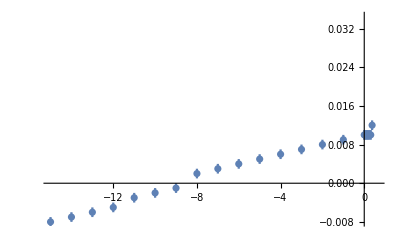

```mathematica
ErrorListPlot[{{#1,#2},ErrorBarPlots`ErrorBar@@{#3,#4}}&@@@data,PlotRangePadding->{Scaled[0.15],Automatic}]
```

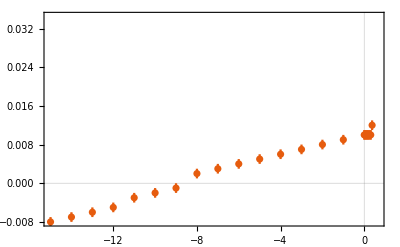

```mathematica
ErrorListPlot[Apply[{{#1,#2},ErrorBar@@{#3,#4}}&,data,{1}],PlotTheme->"Scientific",PlotRangePadding->{Scaled[0.15],Automatic}]
```

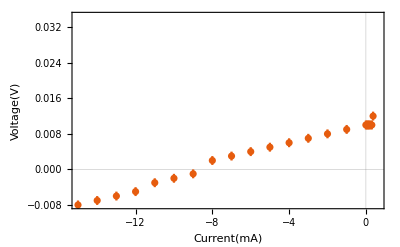

```mathematica
Show[%7,FrameLabel->{{HoldForm[Voltage[V]],None},{HoldForm[Current[mA]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Garamond Premier Pro",15,GrayLevel[0]}]
```

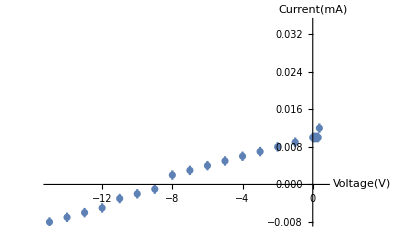

```mathematica
Show[%3,AxesLabel->{HoldForm[Voltage[V]],HoldForm[Current[mA]]},PlotLabel->None,LabelStyle->{FontFamily->"Garamond Premier Pro",15,GrayLevel[0]}]
```

```mathematica
data2:={{0,0.01,0.1,0.001},{0.05,0.01,0.005,0.001},{0.112,0.01,0.008,0.001},{0.168,0.01,0.004,0.001},{0.24,0.01,0.004,0.001},{0.31,0.01,0.002,0.001},{0.376,0.012,0.002,0.001},{0.464,0.037,0.004,0.001},{0.48,0.055,0.004,0.001},{0.528,0.18,0.004,0.005},{0.632,1.74,0.004,0.005}}
```

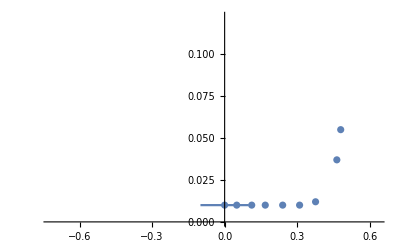

```mathematica
ErrorListPlot[{{#1,#2},ErrorBarPlots`ErrorBar@@{#3,#4}}&@@@data2,PlotRangePadding->{Scaled[0.15],Automatic}]
```

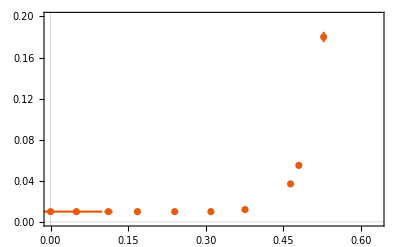

```mathematica
ErrorListPlot[Apply[{{#1,#2},ErrorBar@@{#3,#4}}&,data2,{1}],PlotTheme->"Scientific",PlotRangePadding->{Scaled[0.15],Automatic},PlotRange->{0,0.2}]
```

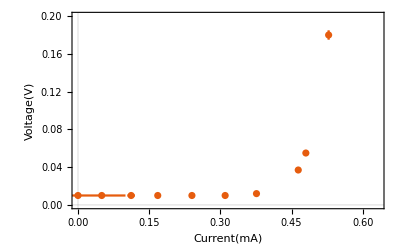

```mathematica
Show[%30,FrameLabel->{{HoldForm[Voltage[V]],None},{HoldForm[Current[mA]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Garamond Premier Pro",15,GrayLevel[0]}]
```